# 透視投影の理解を深めよう

## 関数の定義

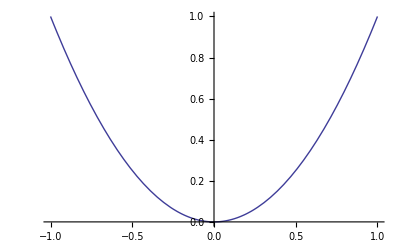

```mathematica
Plot[x^2,{x,-1,1}]
```

```mathematica
f[x_]:=x^2
```

```mathematica
Plot[f[x],{x,-1,1}]
```

-Graphics-

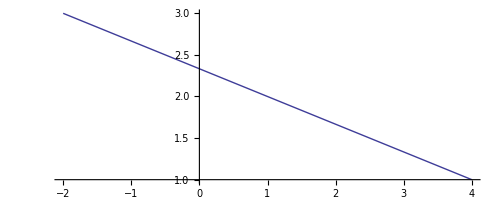

```mathematica
ParametricPlot[{1,2}+t*{-3,1},{t,-1,1}]
```

```mathematica
line1[t_]:={1,2}+t*{-3,1}
```

```mathematica
ParametricPlot[line1[t],{t,-1,1}]
```

-Graphics-

## 透視投影

```mathematica
perspective[a_,b_,c_,d_][v1_,v2_,v3_][x_,y_,z_]:={x,y,z}+(d-(a*x+b*y+c*z))/(a(v1-x)+b(v2-y)+c(v3-z))({v1,v2,v3}-{x,y,z})
```

視点が V(10, 2, 3)，投影面が yz - 平面（つまり，x=0）の透視投影．P(-8, 2, 3) の像は？

```mathematica
perspective[1,0,0,0][10,2,3][-8,2,3]
```

{0,2,3}

視点 V，投影面 yz - 平面，点Pと投影像を描画すると

```mathematica
Show[
Graphics3D[Point[{10,2,3}]],
Graphics3D[Point[{-8,2,3}]],
Graphics3D[Point[perspective[1,0,0,0][10,2,3][-8,2,3]]],
ContourPlot3D[x==0,{x,-10,10},{y,-10,10},{z,-10,10}]
]
```

-Graphics3D-

投影像の点を大きくする．平面のメッシュを描かない．

```mathematica
Show[
Graphics3D[Point[{10,2,3}]],
Graphics3D[Point[{-8,2,3}]],
Graphics3D[{PointSize[0.03],Point[perspective[1,0,0,0][10,2,3][-8,2,3]]}],
ContourPlot3D[x==0,{x,-10,10},{y,-10,10},{z,-10,10},Mesh->False]
]
```

-Graphics3D-

## [問題C]

投影面を変えなさい．

投影する点を増やしなさい．

三角形の投影像を描画しなさい．

Manipulate コマンドを使って，動く絵を作りなさい．